```mathematica
ConditionRayleigh=l2dR   (*hsa to be positive for stability*)
BruntVaisala=-1/(γ*ρ[Rper,zper])(PdR[Rper,zper]*σdR[Rper,zper]+Pdz[Rper,zper]*σdz[Rper,zper]);
Condition1 = BruntVaisala+Rper*Ω2dR     (*has to be positive for stability*)

SolbergHoiland=l2dR*σdz[Rper,zper]-l2dz*σdR[Rper,zper];
ConditionSH = -Pdz[Rper,zper]*SolbergHoiland      (*has to be positive for stability*)

Balbus1995=Ω2dR*σdz[Rper,zper]-Ω2dz*σdR[Rper,zper];
ConditionBalb= -Pdz[Rper,zper]*Balbus1995        (*has to be positive for stability*)
```

1.08798×10^21

1.10745×10^-6

2.21964×10^14

9.38297×10^-30

```mathematica
DispersionRelationGS:=q^3+q^2*((2*ν*k[t]^2)/Ω[Rper,zper]+(ξradiative*k[t]^2)/(γ*Ω[Rper,zper]))+q*((kz[t]/k[t])^2*1/(γ*Ω[Rper,zper]^2 ρ[Rper,zper])*(PdR[Rper,zper]+ρ[Rper,zper]*Ω[Rper,zper]^2*Rper-kR[t]/kz[t] Pdz[Rper,zper])(kR[t]/kz[t] σdz[Rper,zper]-σdR[Rper,zper])+2/(Ω[Rper,zper]*Rper)(kz[t]/k[t])^2(ldR-kR[t]/kz[t] ldz)+2/γ*((ξradiative*k[t]^2)/Ω[Rper,zper])((ν*k[t]^2)/Ω[Rper,zper])+((ν*k[t]^2)/Ω[Rper,zper])^2)+((kz[t]/k[t])^2*1/(γ*Ω[Rper,zper]^2 ρ[Rper,zper])*((ν*k[t]^2)/Ω[Rper,zper])(PdR[Rper,zper]+ρ[Rper,zper]*Ω[Rper,zper]^2*Rper-kR[t]/kz[t] Pdz[Rper,zper])(kR[t]/kz[t] σdz[Rper,zper]-σdR[Rper,zper])+2/(γ*Ω[Rper,zper]*Rper)(kz[t]/k[t])^2((ξradiative*k[t]^2)/Ω[Rper,zper])(ldR-kR[t]/kz[t] ldz)+1/γ((ξradiative*k[t]^2)/Ω[Rper,zper])((ν*k[t]^2)/Ω[Rper,zper])^2)==0
```

```mathematica
Mu=0.62;
γ=5/3;
ν=0;

kRoss=21.1; (* Rosseland opacity at 0.7 Rsun*)
χ=10^3*((16*T[Rper,zper]^3*sigmaSB*(γ-1)*Mu*mP)/(3*kRoss*ρ[Rper,zper]^2*kB))   (*this is what Goldreich and Schubert call χ*)
ξradiative = (γ-1)*χ   (*this is what Balbus and Schaan call ξrad*)

(*ξradiative=1.2*10^7
χ=1/(γ-1)*P[Rper,zper]/T[Rper,zper]*ξradiative*)
η=0;
kMod=(2Pi)/(10^-5 Rsun);

k[t_]:=(kR[t]^2+kϕ[t]^2+kz[t]^2)^(1/2);

kR[t_]:=kR0;
kϕ[t_]:=kϕ0;
kz[t_]:=kz0;
```

2.13929×10^10

1.42619×10^10

```mathematica
rper:=0.7Rsun;
θper:=45*Pi/180;
Rper:=rper*Cos[θper];
zper:=rper*Sin[θper];
ΩdR[Rper,zper]
Ωdz[Rper,zper]
```

-8.36874×10^-18

-1.8117×10^-17

```mathematica
Nαk=601;
FrequenzeAdimensionali=Table[
kR0=kMod*Sin[αk];
kϕ0=0;
kz0=kMod*Cos[αk];

SoluzioniGS=NSolve[DispersionRelationGS/.{t->0},q];
{αk,Maxw=Sort[Re[q/.SoluzioniGS],#1>#2&][[1]]},{αk,Pi*1/Nαk,Pi(1-1/Nαk),Pi*1/Nαk}];
FrequenzeAdimensionaliSorted=Sort[FrequenzeAdimensionali,#1[[2]]>#2[[2]]&];

FrequenzeAdimensionaliSorted[[1]]
```

{(312 π)/601,0.0389365}

```mathematica
PredictedGrowthTimescale=1/(FrequenzeAdimensionaliSorted[[1]][[2]]Ω[Rper,zper])
```

9.68275×10^6

```mathematica
αk=FrequenzeAdimensionaliSorted[[1]][[1]]
kR0:=kMod*Sin[αk]
kϕ0=0;
kz0:=kMod*Cos[αk]

kModGrowthTimescaleList=Table[kMod=(2Pi)/(10^-i Rsun);
GrowthTimescale=1/(Ω[Rper,zper]*q/.NSolve[DispersionRelationGS/.{t->0},q][[3]]);
{kMod,GrowthTimescale},{i,1,9}]
```

(312 π)/601

{{9.02782×10^-10,8.67516×10^14},{9.02782×10^-9,8.67516×10^12},{9.02782×10^-8,8.67516×10^10},{9.02782×10^-7,8.67527×10^8},{9.02782×10^-6,9.68275×10^6},{0.0000902782,3.16719×10^6},{0.000902782,3.12394×10^6},{0.00902782,3.12352×10^6},{0.0902782,3.12351×10^6}}

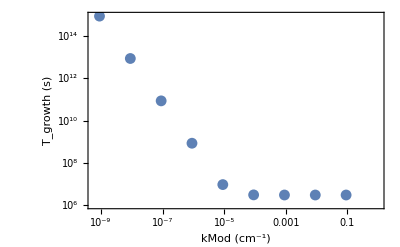

```mathematica
ListLogLogPlot[kModGrowthTimescaleList,Frame->True,FrameLabel->{"kMod (cm^-1)","T_growth (s)"},BaseStyle->{FontWeight->"Bold",FontSize->16}]
```

```mathematica
kR0=-10^-5.5;
kz0=10^-7.5;
ν=0;
NSolve[DispersionRelationGS/.{t->0},q]

ν=23;
NSolve[DispersionRelationGS/.{t->0},q]
```

{{q→-32262.3},{q→-2.49008},{q→0.00173796}}

{{q→-32262.3},{q→-2.49016},{q→0.00165124}}

```mathematica
rper:=0.7Rsun;
θper:=45*Pi/180;
Rper:=rper*Cos[θper];
zper:=rper*Sin[θper];

kR0=-10^-4;
kz0=10^-7;
ν=0;
NSolve[DispersionRelationGS/.{t->0},q]

ν=23;
NSolve[DispersionRelationGS/.{t->0},q]
```

{{q→-3.22616×10^7},{q→-0.0228628},{q→0.0204183}}

{{q→-3.22616×10^7},{q→-0.109576},{q→-0.0662948}}

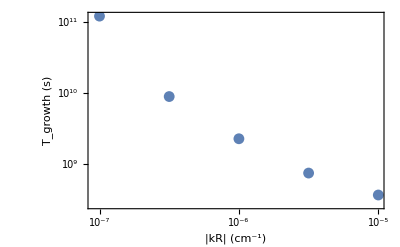

```mathematica
kR0:=-10^i
kϕ0=0;
kz0:=10^-8;

kModGrowthTimescaleList=Table[GrowthTimescale=1/(Ω[Rper,zper]*q/.NSolve[DispersionRelationGS/.{t->0},q][[3]]);
{-i,GrowthTimescale},{i,-8,-4,0.5}];
kModGrowthTimescalePositiveList1=Table[{10^i,1/(Ω[Rper,zper]*q/.NSolve[DispersionRelationGS/.{t->0},q][[3]])},{i,-7,-5,0.5}];
ListLogLogPlot[kModGrowthTimescalePositiveList1,Frame->True,FrameLabel->{"|kR| (cm^-1)","T_growth (s)"},BaseStyle->{FontWeight->"Bold",FontSize->16}]
```

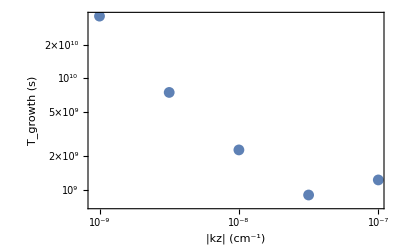

```mathematica
kR0:=-10^-6;
kϕ0=0;
kz0:=10^i;

kModGrowthTimescaleList=Table[{10^i,q/.NSolve[DispersionRelationGS/.{t->0},q][[3]]},{i,-10,-6,0.5}];
kModGrowthTimescalePositiveList2=Table[{10^i,1/(Ω[Rper,zper]*q/.NSolve[DispersionRelationGS/.{t->0},q][[3]])},{i,-9,-7,0.5}];
ListLogLogPlot[kModGrowthTimescalePositiveList2,Frame->True,FrameLabel->{"|kz| (cm^-1)","T_growth (s)"},BaseStyle->{FontWeight->"Bold",FontSize->16}]
```

```mathematica
kR0=-10^-5;
kz0=10^-6;
ν=0;
NSolve[DispersionRelationGS/.{t->0},q]

ν=23;
NSolve[DispersionRelationGS/.{t->0},q]
1/(Ω[Rper,zper]*q/.NSolve[DispersionRelationGS/.{t->0},q][[3]])
```

{{q→-325842.},{q→-0.318116},{q→0.0287398}}

{{q→-325842.},{q→-0.318992},{q→0.027864}}

1.35305×10^7